# Constructing Term Structure -- Nelson-Siegel

## Equal Weighted

```mathematica
α = 1;
```

```mathematica
R[t_, β0_, β1_, β2_] := β0 + β1 *(1-ⅇ^(-α*t))/(α * t) + β2*(1 - (1 + α * t)*ⅇ^(-α * t))/(α * t);
```

```mathematica
B[t_, β0_, β1_, β2_] := ⅇ^(-t*R[t,β0,β1,β2]);
```

```mathematica
Cp[t_, c_, β0_, β1_, β2_] := 0.5 * ∑_(i=1)^(2*t) c * ⅇ^(i/2 R[i/2,β0,β1,β2])+ ⅇ^(-t*R[t,β0,β1,β2]);
```

```mathematica
{b0, b1, b2} =  {β0,β1,β2}/.Minimize[
(1 - Cp[1, 0.78/ 100, β0, β1, β2])^2 +
(1 - Cp[2, 0.91 / 100, β0, β1, β2])^2+
(1 - Cp[5, 1.26 / 100, β0, β1, β2])^2 +(1 - Cp[10, 1.70/ 100, β0, β1, β2])^2 ,{β0, β1, β2}][[2]]
```

{0.0274762,0.00492522,-0.075346}

## Duration weighted

```mathematica
Dur[t_, c_, β0_, β1_, β2_] := ∑_(i=1)^(2*t) (0.5*c *(i/2) *ⅇ^(-(i/2)*R[i/2,β0,β1,β2]))/Cp[t,c,β0,β1,β2]+ (1*t*ⅇ^(-t*R[t,β0,β1,β2]))/Cp[t,c,β0,β1,β2];
```

```mathematica
{B0, B1, B2} =  {β0,β1,β2}/.Minimize[
(1/Dur[1,0.54∕100,β0,β1,β2])*(1 - Cp[1, 0.54/ 100, β0, β1, β2])^2 +
(1∕Dur[2,0.85∕100,β0,β1,β2])*(1 - Cp[2, 0.85 / 100, β0, β1, β2])^2+
(1∕Dur[5, 1.59∕100,β0,β1,β2])*(1 - Cp[5, 1.59 / 100, β0, β1, β2])^2 +(1∕Dur[10, 2.22∕100,β0,β1,β2])*(1 - Cp[10, 2.22/ 100, β0, β1, β2])^2 ,{β0, β1, β2}][[2]]
```

{0.0383766,-0.0122485,-0.0896862}

## Plot

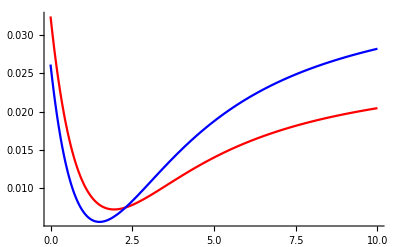

```mathematica
Plot[{R[t,b0,b1,b2],R[t,B0,B1,B2]},{t,0,10},PlotStyle->{Red,Blue}]
```

## Coupon Price

```mathematica
Cp[5, 5 / 100, b0, b1, b2]
```

1.19014

```mathematica
y/.Solve[5*(ⅇ^(-0.5y)+ⅇ^-y+ⅇ^(-1.5y)+ⅇ^(-2y)+ⅇ^(-2.5y)+ⅇ^(-3y)+ⅇ^(-3.5y)+ⅇ^(-4y)+ⅇ^(-4.5y)+ⅇ^(-5y))+100*ⅇ^(-5y)==118.012,y,Reals];
```

## 3. (d)

```mathematica
rr=r/.Solve[∑_(i=11)^20 0.5*0.05*ⅇ^(-r(0.5*i-5))+1*ⅇ^(-r*5)==1,r,Reals];
```

```mathematica
Array[k,10];
```

```mathematica
Do[k[i-10]=ⅇ^(-rr(i/2-5)),{i,11,20,1}];
```

```mathematica
Array[v,10];
```

```mathematica
κ=0.9;
σ=0.1;
```

```mathematica
Do[v[i-10]=1/(2*κ)*σ/κ*ⅇ^(-κ(i/2-5))*(1-ⅇ^(-2κ-5)),{i,11,20,1}]
```

```mathematica
Array[d1,10];
Array[d2,10];
```

```mathematica
Do[d1[i-10]=1/v[i-10]*Log[B[i/2,b0,b1,b2]/(k[i-10]*B[5,b0,b1,b2])]+v[i-10]/2,{i,11,20,1}]
```

```mathematica
Do[d2[i-10]=1/v[i-10]*Log[B[i/2,b0,b1,b2]/(k[i-10]*B[5,b0,b1,b2])]-v[i-10]/2,{i,11,20,1}]
```

```mathematica
t=5;
```

```mathematica
Poption=∑_(i=1)^(2t) Boole[5<i/2]*0.5*0.05*(B[i/2,b0,b1,b2]*CDF[NormalDistribution[0,1],d1[i-10]]-k[i-10]*B[5,b0,b1,b2]*CDF[NormalDistribution[0,1],d2[i-10]])+(B[10,b0,b1,b2]*CDF[NormalDistribution[0,1],d1[10]]-k[10]*B[5,b0,b1,b2]*CDF[NormalDistribution[0,1],d2[10]])
```

{0.0867493}

```mathematica
Pcall= (Cp[5, 5 / 100, b0, b1, b2]-Poption)
```

{1.10339}

## 4. (g)

```mathematica
ω=0.38;
```

```mathematica
γ=-1.5;
```

```mathematica
t=0;
```

```mathematica
Vt=Φ=(∫_t^5 (ω(5-s)ⅇ^(γ(5-s)))^2 ⅆs)^(1/2);
```

```mathematica
Ft=(B[5,b0,b1,b2]-B[10,b0,b1,b2])/(∑_(i=1)^10 (0.5B[5+0.5i,b0,b1,b2]));
```

```mathematica
kk=5/100;
```

```mathematica
dt1=1/Vt Log[Ft/kk]+1/2 Vt;
```

```mathematica
dt2=1/Vt Log[Ft/kk]-1/2 Vt;
```

```mathematica
Bput[Ft_,kk_,Vt_,dt1_,dt2_]:=kk*CDF[NormalDistribution[0,1],-dt2]-Ft*CDF[NormalDistribution[0,1],-dt1];
```

```mathematica
A0=∑_(i=1)^10 0.5B[5+0.5i,b0,b1,b2];
```

```mathematica
Pswaption=A0*Bput[Ft,kk,Vt,dt1,dt2]
```

0.0995704

```mathematica
Cp[5, 5 / 100, b0, b1, b2]-Pswaption
```

1.09056

## 3. (h)

```mathematica
5000000/(Cp[5, 5 / 100, b0, b1, b2]-Pswaption)
```

4.58478×10^6